```mathematica
u[n_,t_]:=A*Exp[I*(k*n*a-w*t)]
```

```mathematica
c1(u[n-1,t]-2u[n,t]+u[n+1,t])+c2(u[n-2,t]-2u[n,t]+u[n+2,t])
```

c1 (A ⅇ^(ⅈ (a k (-1+n)-t w))-2 A ⅇ^(ⅈ (a k n-t w))+A ⅇ^(ⅈ (a k (1+n)-t w)))+c2 (A ⅇ^(ⅈ (a k (-2+n)-t w))-2 A ⅇ^(ⅈ (a k n-t w))+A ⅇ^(ⅈ (a k (2+n)-t w)))

```mathematica
Solve[FullSimplify[c1 (A ⅇ^(ⅈ (a k (-1+n)-t w))-2 A ⅇ^(ⅈ (a k n-t w))+A ⅇ^(ⅈ (a k (1+n)-t w)))+c2 (A ⅇ^(ⅈ (a k (-2+n)-t w))-2 A ⅇ^(ⅈ (a k n-t w))+A ⅇ^(ⅈ (a k (2+n)-t w)))]/(A*Exp[I(k*n*a-w*t)])==-m*w^2,w]
```

{{w→-(2 √(c1+2 c2+2 c2 Cos[a k]) Sin[(a k)/2])/(√m)},{w→(2 √(c1+2 c2+2 c2 Cos[a k]) Sin[(a k)/2])/(√m)}}

```mathematica
(2 √(c1+FullSimplify[2 c2+2 c2 Cos[a k]]) Sin[(a k)/2])/(√m)==(2 √(Sin[(a k)/2]^2(c1+2 c2+2 c2 Cos[a k])))/(√m)
```

(2 √(c1+2 c2 (1+Cos[a k])) Sin[(a k)/2])/(√m)==(2 √((c1+2 c2+2 c2 Cos[a k]) Sin[(a k)/2]^2))/(√m)

```mathematica
Solve[{FullSimplify[c1 (A ⅇ^(ⅈ (a k (-1+n)-t w))-2 A ⅇ^(ⅈ (a k n-t w))+A ⅇ^(ⅈ (a k (1+n)-t w)))+c2 (A ⅇ^(ⅈ (a k (-2+n)-t w))-2 A ⅇ^(ⅈ (a k n-t w))+A ⅇ^(ⅈ (a k (2+n)-t w)))]/(A*Exp[I(k*n*a-w*t)])==-m*w^2},w]/.c2->(0.1*c1)
```

{{w→-(2 √(1.2 c1+0.2 c1 Cos[a k]) Sin[(a k)/2])/(√m)},{w→(2 √(1.2 c1+0.2 c1 Cos[a k]) Sin[(a k)/2])/(√m)}}

{-0.0542245,-0.0561831,-0.0586154,-0.0602264,-0.0616341,-0.0632368,-0.0630106,-0.0636321,-0.0637822,-0.0654694,-0.0650206,-0.0651231,-0.0637805,-0.0643212,-0.064136,-0.062838,-0.0624245,-0.0616178,-0.0611359,-0.0598227,-0.0591423}

0.147085-0.166425 x+0.0326574 x^2

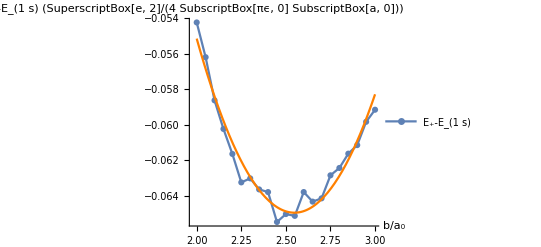

```mathematica
(*Question 1a*)
Clear["Global`*"]
data=Import["C:\\Users\\pbuttles\\Downloads\\H2_ion,S,J,K_NearMinimum.csv"];
data=Drop[data,2];
data=Drop[data,8];
data=Drop[data,-6];
ba0[i_]:=data[[i,1]]
Sdata[i_]:=data[[i,2]]
J[i_]:=data[[i,3]]
K[i_]:=data[[i,4]]
V[i_]:=data[[i,5]]
eplus={};
eminus={};
xvals={};
For[i=1,i≤21,i++,AppendTo[eplus,V[i]+(J[i]+K[i])/(1+Sdata[i])]]
For[i=1,i≤21,i++,AppendTo[eminus,V[i]+(J[i]-K[i])/(1+Sdata[i])]]
For[i=1,i≤21,i++,AppendTo[xvals,ba0[i]]]
eplus
plot1 = ListLinePlot[{Transpose[{xvals,eplus}]},PlotLegends->{"E_+-E_(1  s)","E_+-E_(1  s)"},AxesLabel->{"b/a_0","E_±-E_(1  s) (SuperscriptBox[e, 2]/(4 SubscriptBox[πϵ, 0] SubscriptBox[a, 0]))"},PlotMarkers->Automatic];
Fit[Transpose[{xvals,eplus}],{1,x,x^2},x]
plot2=Plot[%,{x,2,3},PlotStyle->Orange];
Show[plot1,plot2]
```

```mathematica
2*0.03265744880141224
```

0.0653149

```mathematica
27.2*√(2*0.06531*(1/1836))
```

0.229423

```mathematica
0.2294232381913877/(6.582*10^-16)
```

3.48562×10^14

```mathematica
Solve[2*Sin[ka/2]==0.026,ka]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ka→0.0260007}}

```mathematica
(2*0.026)/π
```

0.0165521

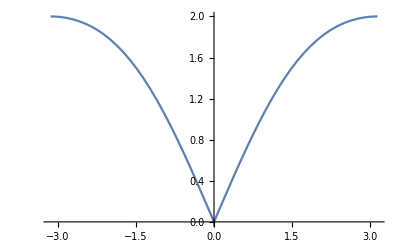

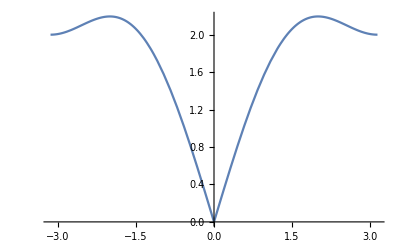

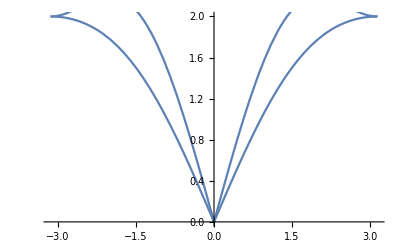

```mathematica
(*Question 2*)
c2overc1=0.1;
p1=Plot[Abs[2*Sin[ka/2] √(1+2*c2overc1(1+Cos[ka]))],{ka,-π,π}]
c2overc1=0.6;
p2=Plot[Abs[2*Sin[ka/2] √(1+2*c2overc1(1+Cos[ka]))],{ka,-π,π}]
Show[p1,p2]
```

```mathematica
w[k_]:=2*Sin[(k*a)/2] √(c1/m)√(1+2*c2/c1(1+Cos[k*a]))
FullSimplify[D[w[k],k]]
```

(a √(c1/m) Cos[(a k)/2] (c1+4 c2 Cos[a k]))/(c1 √((c1+2 c2+2 c2 Cos[a k])/c1))

```mathematica
(*Question 4*)
Clear["Global`*"]
u[n_,t_]:=A*Exp[I*(k*n*a-w*t)]
v[n_,t_]:=B*Exp[I*(k*n*a-w*t)]
D[D[u[n,t],t],t]
D[D[v[n,t],t],t]
Simplify[(c1*(v[n,t]-u[n,t])-c2*(u[n,t]-v[n-1,t]))/(u[n,t])]
Simplify[(c2*(u[n+1,t]-v[n,t])-c1*(v[n,t]-u[n,t]))/(v[n,t])]
```

-A ⅇ^(ⅈ (a k n-t w)) w^2

-B ⅇ^(ⅈ (a k n-t w)) w^2

(-A (c1+c2)+B (c1+c2 ⅇ^(-ⅈ a k)))/A

(-B (c1+c2)+A (c1+c2 ⅇ^(ⅈ a k)))/B

```mathematica
M={{m*w^2-c1-c2,(c1+c2*Exp[-I*k*a])},{(c1+c2*Exp[I*k*a]),m*w^2-c1-c2}}
```

{{-c1-c2+m w^2,c1+c2 ⅇ^(-ⅈ a k)},{c1+c2 ⅇ^(ⅈ a k),-c1-c2+m w^2}}

```mathematica
FullSimplify[Solve[FullSimplify[Det[M]]==0,w]]
```

{{w→-√(((c1+c2) m-√(m^2 (c1^2+c2^2+2 c1 c2 Cos[2 a k])))/m^2)},{w→√(((c1+c2) m-√(m^2 (c1^2+c2^2+2 c1 c2 Cos[2 a k])))/m^2)},{w→-√(((c1+c2) m+√(m^2 (c1^2+c2^2+2 c1 c2 Cos[2 a k])))/m^2)},{w→√(((c1+c2) m+√(m^2 (c1^2+c2^2+2 c1 c2 Cos[2 a k])))/m^2)}}

```mathematica
M={{m*w^2-c1-c2,Exp[-I*k*a]*(c2+c1*Exp[2*I*k*a])},{Exp[-I*k*a]*(c1+c2*Exp[I*2*k*a]),m*w^2-c1-c2}}
```

{{-c1-c2+m w^2,ⅇ^(-ⅈ a k) (c2+c1 ⅇ^(2 ⅈ a k))},{ⅇ^(-ⅈ a k) (c1+c2 ⅇ^(2 ⅈ a k)),-c1-c2+m w^2}}

```mathematica
Solve[FullSimplify[Det[M]]==0,w]/.c2->(2*c1)
```

{{w→-√((3 c1)/m-(√(m^2 (5 c1^2+4 c1^2 Cos[2 a k])))/m^2)},{w→√((3 c1)/m-(√(m^2 (5 c1^2+4 c1^2 Cos[2 a k])))/m^2)},{w→-√((3 c1)/m+(√(m^2 (5 c1^2+4 c1^2 Cos[2 a k])))/m^2)},{w→√((3 c1)/m+(√(m^2 (5 c1^2+4 c1^2 Cos[2 a k])))/m^2)}}

```mathematica
Simplify[(√(m^2 (c1^2+c2^2+2 c1 c2 Cos[2 a k])))/m^2]
```

(√(m^2 (c1^2+c2^2+2 c1 c2 Cos[2 a k])))/m^2

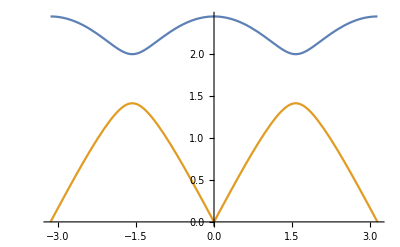

```mathematica
Plot[{√(3+√(5+4*Cos[2*x])),√(3-√(5+4*Cos[2*x]))},{x,-π,π}]
```

```mathematica
√(3+√(5+4*Cos[2*x]))/.x->π/2
√(3-√(5+4*Cos[2*x]))/.x->π/2
```

2

√2